```mathematica
"tangens and arctan approximation - check documentation for details";
```

```mathematica
"tangens:"
im[a_]:=34459425*a-4729725*a^3+135135*a^5-990a^7 +a^9
st[a_]:=34459425-16216200*a^2 +945945a^4-13860*a^6+45*a^8
```

tangens:

```mathematica
T9[a_]:=im[a]/st[a]
```

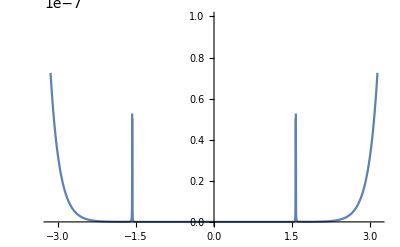

```mathematica
Plot[Abs[T9[a]-Tan[a]],{a, -Pi, Pi}, PlotRange->{0, 10^-7}]
```

```mathematica
SetPrecision[Tan[{-0.7, -0.3, 0.33, 1.553}], 20]
SetPrecision[im[{-0.7, -0.3, 0.33, 1.553}], 20]
```

{-0.84228838046307941134,-0.30933624960962324835,0.3425248675300389678,56.185438688872594071}

{-2.252193247404660657×10^7,-1.0210453086556682363×10^7,1.1202166556932132691×10^7,3.699934455378305167×10^7}

```mathematica
S[n_, t_]:=Block[{},
expression=Collect[Integrate[LegendreP[11,t]*Sin[t],t], Cos[t]];
k=expression/.Cos[t]->0/.Sin[t]->1;
l=expression/.Cos[t]->1/.Sin[t]->0;
Return[l/k]
]
```

```mathematica
S[5,t]
```

(3604742431983 t-600790405215 t^3+30039519510 t^5-715224510 t^7+9930635 t^9-88179 t^11)/(33 (-109234619151+54617309565 t^2-4551442350 t^4+151714290 t^6-2708355 t^8+29393 t^10))

```mathematica
"ArcTan:"
```

ArcTan:

```mathematica
ClearAll[expression, F]
F[n_,a_]:=Block[{arctan1a,arctan,expression, A1, A2},
expression=Collect[Assuming[a∈Reals,Integrate[LegendreP[2*n,t]/(t^2+a^2),{t,0,1}]]/.ArcCot[a]->ArcTan[1/a], ArcTan[1/a]][[1]];
(*Print[expression];*)
A1=(expression[[1]]);
(*Print["A1: ",A1];*)
A2=(expression[[2]]/.ArcCot[a]->ArcTan[1/a])/.ArcTan[1/a]->1;
(*Print["A2: ",A2];*)
arctan1a=-(A1/A2);
arctan=arctan1a/.a->(1/a);
Return[arctan];
]
```

```mathematica
f1=F[1,a]//Simplify
```

(3 a)/(3+a^2)

```mathematica
f1=F[1,a]//Simplify
f2=F[2,a]//Simplify
f3=F[3,a]//Simplify
f4=F[4,a]//Simplify
f5=F[5,a]//Simplify
f6=F[6,a]//Simplify
f9=F[9,a]
```

(3 a)/(3+a^2)

(5 a (21+11 a^2))/(105+90 a^2+9 a^4)

(7 a (165+170 a^2+33 a^4))/(5 (231+315 a^2+105 a^4+5 a^6))

(a (225225+345345 a^2+147455 a^4+15159 a^6))/(35 (6435+12012 a^2+6930 a^4+1260 a^6+35 a^8))

(11 a (1322685+2691780 a^2+1800162 a^4+437580 a^6+27985 a^8))/(315 (46189+109395 a^2+90090 a^4+30030 a^6+3465 a^8+63 a^10))

-(-995215/231-(13 (341195+(51 (45885+116375 a^2+106362 a^4+42054 a^6))/a^8))/(45 a^2))/(231 a+(13 (52003+149226 a^2+159885 a^4+78540 a^6+17325 a^8+1386 a^10))/a^11)

-(4147223271/12155+(19 (2836839936+(253 (170468424+(13 (88833960+(609 (1048944+(155 (7728+1155/a^4+4664/a^2))/a^2))/a^4+317132530/a^2))/a^2))/a^2))/(3003 a^2))/(-(57 (36465+(23 (476476+(5 (510510+(29 (92820+(31 (3060+385/a^4+1683/a^2))/a^2))/a^4+1531530/a^2))/a^2))/a^4+1021020/a^2))/a-12155 a)

```mathematica
"single precision";
f6=F[6,a]//FullSimplify//Expand//Simplify
st=13 a (180190395+457004625 a^2+417683574 a^4+165146058 a^6+26272015 a^8+1148325 a^10);
im=3465 (676039+1939938 a^2+2078505 a^4+1021020 a^6+225225 a^8+18018 a^10+231 a^12);
CoefficientList[st,a]
CoefficientList[im,a]
```

(13 a (180190395+457004625 a^2+417683574 a^4+165146058 a^6+26272015 a^8+1148325 a^10))/(3465 (676039+1939938 a^2+2078505 a^4+1021020 a^6+225225 a^8+18018 a^10+231 a^12))

{0,2342475135,0,5941060125,0,5429886462,0,2146898754,0,341536195,0,14928225}

{2342475135,0,6721885170,0,7202019825,0,3537834300,0,780404625,0,62432370,0,800415}

```mathematica
ArcTan[{0.4,-0.3,-1.4,-1.27}]
```

{0.380506,-0.291457,-0.950547,-0.903785}

```mathematica
"double precision";
f9=F[9,a]//FullSimplify//Expand//FullSimplify
```

(19 a (30479916592125+123080806048200 a^2+203938351016400 a^4+178588049880240 a^6+88659155749450 a^8+24834866027400 a^10+3665923458120 a^12+241131394560 a^14+4583773089 a^16))/(255255 (2268783825+17 a^2 (583401555+1060730100 a^2+13 a^4 (79839900+11 a^2 (4129650+1376550 a^2+256956 a^4+23940 a^6+855 a^8+5 a^10)))))

```mathematica
st=19 a (30479916592125+123080806048200 a^2+203938351016400 a^4+178588049880240 a^6+88659155749450 a^8+24834866027400 a^10+3665923458120 a^12+241131394560 a^14+4583773089 a^16);
im=255255(2268783825+17 a^2 (583401555+1060730100 a^2+13 a^4 (79839900+11 a^2 (4129650+1376550 a^2+256956 a^4+23940 a^6+855 a^8+5 a^10))));
CoefficientList[im,a]
CoefficientList[st,a]
```

{579118415250375,0,2531574786665925,0,4602863248483500,0,4503876942064500,0,2562550673933250,0,854183557977750,0,159447597489180,0,14855366225700,0,530548793775,0,3102624525}

{0,579118415250375,0,2338535314915800,0,3874828669311600,0,3393172947724560,0,1684523959239550,0,471862454520600,0,69652545704280,0,4581496496640,0,87091688691}

```mathematica
2^52
```

4503599627370496

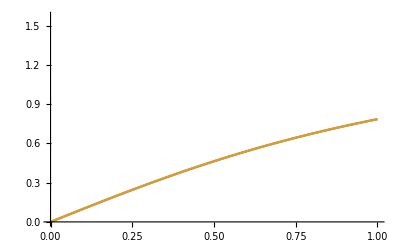

```mathematica
Plot[{
ArcTan[x],
f6/.a->x,
f8/.a->x
},{x,0,1},PlotRange->{0,Pi/2}]
```

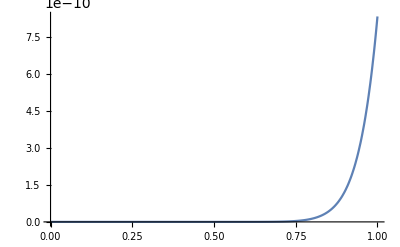

```mathematica
Plot[{
Abs[ArcTan[x]-f6/.a->x]
},{x,0,1},PlotRange->All]
```

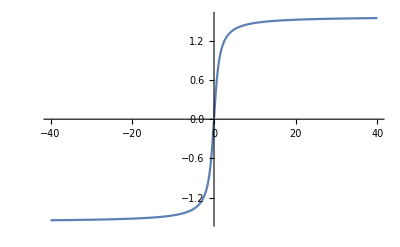

```mathematica
Plot[{
ArcTan[x]
},{x,-40,40},PlotRange->{-Pi/2,Pi/2}]
```